```mathematica
Supplimentary code for :
Sharp decomposition of interdependent multiplex networks by percolation
I.Kryven and G. Bianconi
```

```mathematica
SetDirectory[NotebookDirectory[]];

(* Barycentric coordinates transform: *)
ToBarycentricA[x_,y_]:=1-x-y/(√3); 
ToBarycentricB[x_,y_]:=x-y/(√3);
FromBarycentricX[a_,b_]:=1/2 (1-a-b)+b;
FromBarycentricY[a_,b_]:=1/2 √3 (1-a-b);

(* Inverse of order parameter  s[p] *)
pS[S_]:=S/Q[S];
(*Load a custom package by Ted Ersek, see  http://library.wolfram.com/infocenter/Demos/4482/*)
Import["RootSearch.m"] 

(* Find s in (0,1) such that sQ'[s]-Q[s]==0, and Q''[s]<0  *)
Tc0:=Quiet[Block[{sol1,sol2,pos},
sol1=RootSearch[s Q'[s]-Q[s]==0,{s,10^-10,1}];
If[Length[sol1]==0,Return[{}]];
sol2=s/.sol1;
pos=Flatten[Position[Q''[s]/.sol1,_?(#<0&)]];
Return[sol2[[pos]]]
]];

(* Extract a subsequence that is simultaniously descending in p and s*)
Tc:=Block[{ tc,i ,restc,respc,pc},
tc=Tc0;
If[Length[tc]==0,Return[{}]];
pc=pS[tc];
restc={ Last[tc] };
respc={ Last[pc] };
For[i=Length[tc]-1,i>0,i--,
If[pc[[ i ]]<Last[respc],
AppendTo[ restc,tc[[i]] ];
AppendTo[ respc,pc[[i]] ] ];
];
Return[ restc ];
]
pc0:=1/Q'[0];

(* All discontinuous phase transition points *)
pcd:=Re[pS[Tc]];

(* All continuous phase transition points *)
pcc:=If[Min[pcd]>pc0,Join[pcd,pc0],pcd];

(* Number of discontinuous crtitical points for Q[x] := q[1] x^k[1] + q[2] x^k[2] + q[3] x^k[3] *)
CountPCD[a_,b_]:=Block[{},
q[1]=a;
q[2]=b;
q[3]=Max[1 - a - b, 0];
Ek=Sum[q[i]k[i],{i,1,n}];

Return[Catch[Check[Length[Tc],-1]]];
];

(* Number of discontinuous crtitical points for Q[x] := q[1] x^k[1] + q[2] x^k[2] + q[3] x^k[3] *)
CountPCC[a_,b_]:=Block[{},
q[1]=a;
q[2]=b;
q[3]=Max[1 - a - b, 0];
Ek=Sum[q[i]k[i],{i,1,n}];

pc=pc0;
If[pc>0 && pc<Min[pcd],
Return[1],
Return[0]
];

];

(* Recursive equations for order parameter S(p) *)
Q[S_]:= Sum[k[i]q[i]/Ek(1-(1-S)^(k[i]-1))(1-(1-S)^k[i])^(B[i]-1),{i,1,n}];
Q1[S_]:= Sum[q[i](1-(1-S)^k[i])^B[i],{i,1,n}];
Sn[n_,pp_]:=If[n==0,pp,N[ pp Q[Sn[n-1,pp]] ]];
```

# Example 1 : constant activity, variable degree

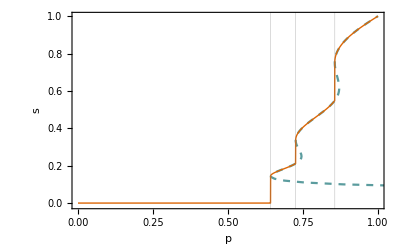

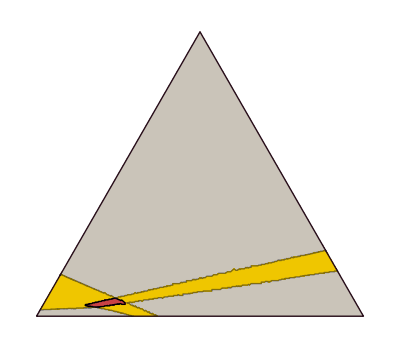

```mathematica
(* Here we define the degree-activity distribution given by three delta peaks with degree k[i], and activity B[i], and weights q[i]; where i=1,2,3 *)
n=3;

k[1]=3;
k[2]=9;
k[3]=30;

B[1]=20;
B[2]=20;
B[3]=20;

q[1]=0.75;
q[2]=0.20;
q[3]=1-q[1]-q[2];

Ek=Sum[q[i]k[i],{i,1,n}];
(*Plot s(p) and the phase diagram*)
h1=ListLinePlot[ Table[{s/Q[s],s},{s,0.05,1,0.01}],PlotStyle->{Dashed,RGBColor[0.3568627450980392, 0.611764705882353, 0.6196078431372549]},PlotRange->{0,1},Frame->True,FrameLabel->{"p","s"}];
h2=Plot[Sn[200,p],{p,0,1},PlotRange->{0,1},PlotStyle->{Thick,RGBColor[0.8627450980392157, 0.403921568627451, 0.027450980392156862]},Frame->True,FrameLabel->{"p","s"}];
Show[h1,h2,PlotRange->{{0,1},{-0.01,1}},Axes->False,GridLines->{pcd,{}}]
colors={RGBColor[0.3568627450980392, 0.611764705882353, 0.6196078431372549, 0],RGBColor[0.792156862745098, 0.7686274509803922, 0.7254901960784313],RGBColor[0.9372549019607843, 0.7764705882352941, 0.],RGBColor[0.79, 0.26, 0.27]};
H2=ContourPlot[ CountPCD[ToBarycentricA[x,y],ToBarycentricB[x,y]],{x,0,1},{y,0,(√3)/2},
		        RegionFunction->Function[{x,y},√3 x>y&&√3(1-x)>y],
		        Contours->{0.01,1.01,2.01},
		        ContourStyle->{Thick,RGBColor[0.0784313725490196, 0.08627450980392157, 0.13725490196078433],Opacity[1]},
	                  PlotPoints ->4,MaxRecursion->3,Frame->False,Mesh->None, (* for beter pressision use PlotPoints ->4, MaxRecursion->4 *)
		         BoundaryStyle->{Thick,RGBColor[0.15294117647058825, 0.050980392156862744, 0.10196078431372549]},ContourShading->colors,ContourStyle->{Thick,Black}
		      ];
Show[H2,AspectRatio->0.87]
SwatchLegend[{RGBColor[0.792156862745098, 0.7686274509803922, 0.7254901960784313],RGBColor[0.9372549019607843, 0.7764705882352941, 0.],RGBColor[0.79, 0.26, 0.27]},{"Ω_01","Ω_02","Ω_03"}]
```

```mathematica
Example 2: constant  degree,  variable activity
```

Power::indet: Indeterminate expression 0.^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

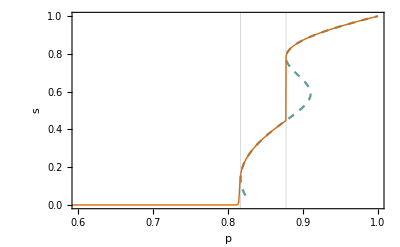

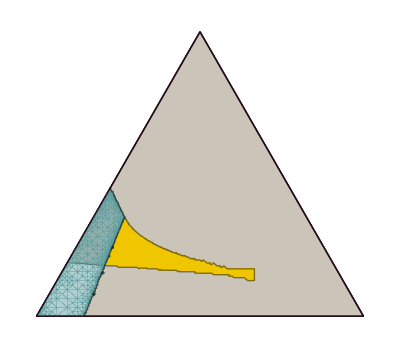

```mathematica
(* Here we define the degree-activity distribution given by three delta peaks with degree k[i], and activity B[i], and weights q[i]; where i=1,2,3 *)
n=3;


k[1]=3;
k[2]=3;
k[3]=3;

B[1]=1;
B[2]=2;
B[3]=30;

q[1]=0.60;
q[2]=0.16;
q[3]=1-q[1]-q[2];

Ek=Sum[q[i]k[i],{i,1,n}];

(*Plot s(p) and the phase diagram*)
h1=ListLinePlot[ Table[{s/Q[s],s},{s,0.03,1,0.01}],PlotStyle->{Dashed,RGBColor[0.3568627450980392, 0.611764705882353, 0.6196078431372549]},PlotRange->{0,1},Frame->True,FrameLabel->{"p","s"}];
h2=Plot[Sn[400,p],{p,0,1},PlotRange->{0,1},PlotStyle->{Thick,RGBColor[0.8627450980392157, 0.403921568627451, 0.027450980392156862]},Frame->True,FrameLabel->{"p","s"}];
Show[h1,h2,PlotRange->{{0.6,1},{0,1}},Axes->False,GridLines->{pcd,{}}]

colors={RGBColor[0.3568627450980392, 0.611764705882353, 0.6196078431372549, 0],RGBColor[0.792156862745098, 0.7686274509803922, 0.7254901960784313],RGBColor[0.9372549019607843, 0.7764705882352941, 0.],RGBColor[0.79, 0.26, 0.27],RGBColor[0.3568627450980392, 0.611764705882353, 0.6196078431372549]};
H0=RegionPlot[{√3 x>y&&√3(1-x)>y},{x,0,1},{y,0,(√3)/2},Frame->False,PlotStyle->RGBColor[0.3568627450980392, 0.611764705882353, 0.6196078431372549, 0],BoundaryStyle->{Thick,Black}];
H1=ContourPlot[ CountPCC[ToBarycentricA[x,y],ToBarycentricB[x,y]],{x,0,1},{y,0,(√3)/2},
		        RegionFunction->Function[{x,y},√3 x>y&&√3(1-x)>y],
		        Contours->{0.01,1.01,2.01},
		        ContourStyle->{Thick,RGBColor[0.0784313725490196, 0.08627450980392157, 0.13725490196078433],Opacity[1]},
	                  PlotPoints ->3,MaxRecursion->3,Frame->False,Mesh->None, 
		          BoundaryStyle->{Thick,RGBColor[0.15294117647058825, 0.050980392156862744, 0.10196078431372549]},ContourShading->{RGBColor[0.3568627450980392, 0.611764705882353, 0.6196078431372549, 0],RGBColor[0.3568627450980392, 0.611764705882353, 0.6196078431372549, 0.48],RGBColor[0.3568627450980392, 0.611764705882353, 0.6196078431372549, 0]},ContourStyle->{Thick,Black}
		      ];
H2=ContourPlot[ CountPCD[ToBarycentricA[x,y],ToBarycentricB[x,y]],{x,0,1},{y,0,(√3)/2},
		        RegionFunction->Function[{x,y},√3 x>y&&√3(1-x)>y],
		        Contours->{0.01,1.01,2.01},
		        ContourStyle->{Thick,RGBColor[0.0784313725490196, 0.08627450980392157, 0.13725490196078433],Opacity[1]},
	                  PlotPoints ->4,MaxRecursion->3,Frame->False,Mesh->None, (* for beter pressision use PlotPoints ->4, MaxRecursion->4 *)
		         BoundaryStyle->{Thick,RGBColor[0.15294117647058825, 0.050980392156862744, 0.10196078431372549]},ContourShading->colors,ContourStyle->{Thick,Black}
		      ];
Show[H0,H2,H1,AspectRatio->0.87]
```